```mathematica
TableForm[Table[Map[Last,FormulaSummary2[FindFullFormula[CompleteGraph[{IntegerPart[Floor[max/2]],max-IntegerPart[Floor[max/2]]}],Table[{k},{k,1,max}]]]],{max,2,12}],TableDepth->2]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 4 | 4 | 1 |  |  |  |  |  |  | 
1 | 6 | 11 | 6 | 1 |  |  |  |  |  | 
1 | 10 | 28 | 26 | 9 | 1 |  |  |  |  | 
1 | 14 | 61 | 86 | 50 | 12 | 1 |  |  |  | 
1 | 22 | 136 | 276 | 236 | 92 | 16 | 1 |  |  | 
1 | 30 | 275 | 770 | 927 | 530 | 150 | 20 | 1 |  | 
1 | 46 | 580 | 2200 | 3551 | 2782 | 1130 | 240 | 25 | 1 | 
1 | 62 | 1141 | 5710 | 12160 | 12632 | 6987 | 2130 | 355 | 30 | 1

```mathematica
With[{max=14},
TableForm[Table[PadRight[Table[StirlingS2[n,k],{k,1,n}],max],{n,1,max}],
TableDepth->2,TableHeadings->{Range[max], Range[max]}]
]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 0 | 0 | 0 | 0 | 0 | 0
9 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 0 | 0 | 0 | 0 | 0
10 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1 | 0 | 0 | 0 | 0
11 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1 | 0 | 0 | 0
12 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1 | 0 | 0
13 | 1 | 4095 | 261625 | 2532530 | 7508501 | 9321312 | 5715424 | 1899612 | 359502 | 39325 | 2431 | 78 | 1 | 0
14 | 1 | 8191 | 788970 | 10391745 | 40075035 | 63436373 | 49329280 | 20912320 | 5135130 | 752752 | 66066 | 3367 | 91 | 1

```mathematica
With[{max=14},
TableForm[Table[PadRight[Table[StirlingS1[n,k],{k,1,n}],max],{n,1,max}],
TableDepth->2,TableHeadings->{Range[max], Range[max]}]
]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 2 | -3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | -6 | 11 | -6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 24 | -50 | 35 | -10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | -120 | 274 | -225 | 85 | -15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 720 | -1764 | 1624 | -735 | 175 | -21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | -5040 | 13068 | -13132 | 6769 | -1960 | 322 | -28 | 1 | 0 | 0 | 0 | 0 | 0 | 0
9 | 40320 | -109584 | 118124 | -67284 | 22449 | -4536 | 546 | -36 | 1 | 0 | 0 | 0 | 0 | 0
10 | -362880 | 1026576 | -1172700 | 723680 | -269325 | 63273 | -9450 | 870 | -45 | 1 | 0 | 0 | 0 | 0
11 | 3628800 | -10628640 | 12753576 | -8409500 | 3416930 | -902055 | 157773 | -18150 | 1320 | -55 | 1 | 0 | 0 | 0
12 | -39916800 | 120543840 | -150917976 | 105258076 | -45995730 | 13339535 | -2637558 | 357423 | -32670 | 1925 | -66 | 1 | 0 | 0
13 | 479001600 | -1486442880 | 1931559552 | -1414014888 | 657206836 | -206070150 | 44990231 | -6926634 | 749463 | -55770 | 2717 | -78 | 1 | 0
14 | -6227020800 | 19802759040 | -26596717056 | 20313753096 | -9957703756 | 3336118786 | -790943153 | 135036473 | -16669653 | 1474473 | -91091 | 3731 | -91 | 1

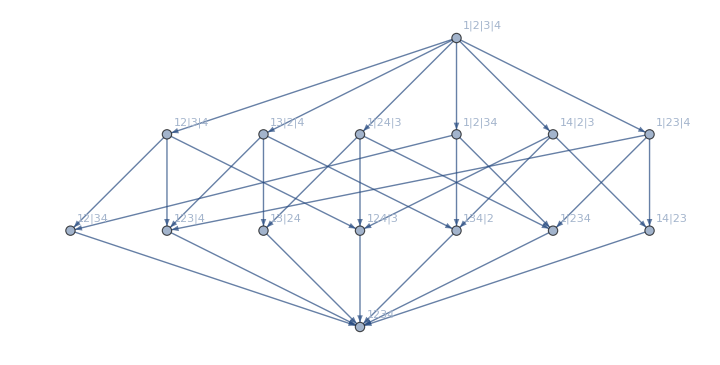
-Graphics-364-Graphics--6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 00024120
-Graphics-

```mathematica
SummaryPrintGood[K4Key]
```